```mathematica
Table[stubbornForm5[k,"comp"]=Equal,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{Equal,Equal,Equal,Equal,Equal}

```mathematica
Table[stubbornForm5[k,"comp"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{Equal,Equal,Equal,Equal,Equal}

```mathematica
Graph[pr]
```

```mathematica
pr=Problems[stubbornForm5,0];
```

```mathematica
Select[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,pr]]],Length[ListofVars[stubbornForm5[#,"colofour"]]]==1&]
```

{36085,29551,31711,29533,38281,29560,38308,29527,29525,36086,29633,36194,30253,36817,30334,36898,29605,29767,31954,29797,31984,49207,51475,49210,51478}

```mathematica
Table[stubbornForm5[k,"colofour"],{k,(Select[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,pr]]],Length[ListofVars[stubbornForm5[#,"colofour"]]]==1&])}]/.repcolofour5base
```

{-Graphics-v13x2x4x5,-Graphics-v1x25x3x4,-Graphics-v14x2x3x5,-Graphics-v1x2x34x5,-Graphics-v134x2x5,-Graphics-v1x25x34,-Graphics-v134x25,-Graphics-v1x2x35x4,-Graphics-v1x2x3x45,-Graphics-v13x2x45,-Graphics-v1x245x3,-Graphics-v13x245,-Graphics-v15x2x3x4,-Graphics-v135x2x4,-Graphics-v15x24x3,-Graphics-v135x24,-Graphics-v1x24x3x5,-Graphics-v1x23x4x5,-Graphics-v14x23x5,-Graphics-v1x235x4,-Graphics-v14x235,-Graphics-v12x3x4x5,-Graphics-v124x3x5,-Graphics-v12x35x4,-Graphics-v124x35}

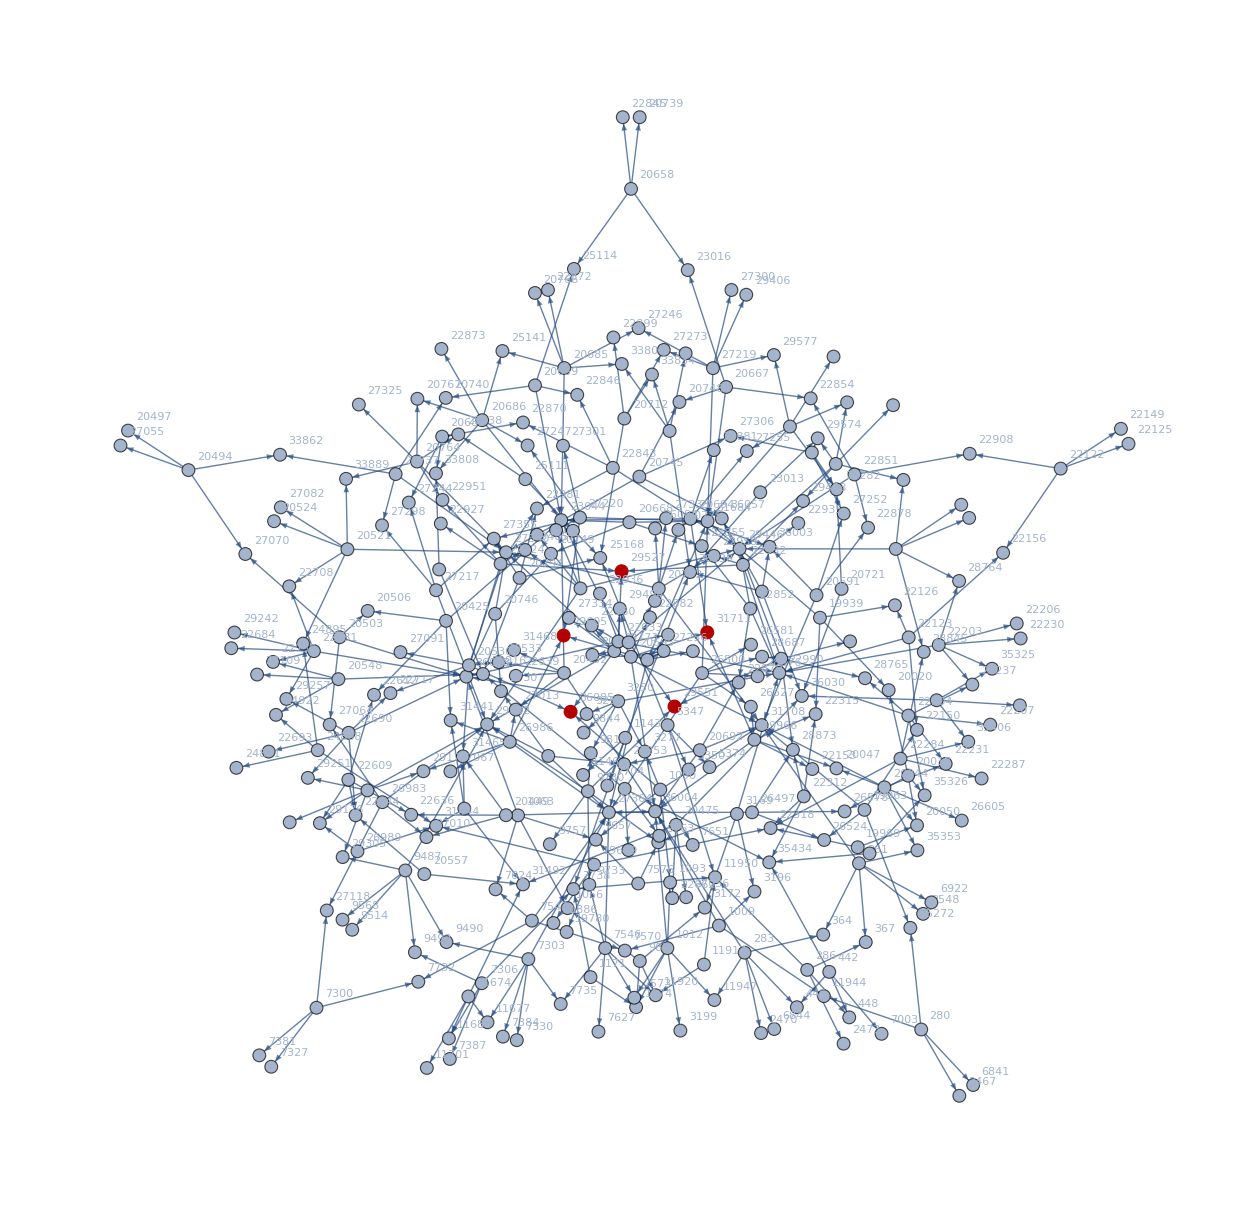

```mathematica
VertexDelete[
Graph[pr,VertexLabels->"Name",GraphHighlight->Select[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,pr]]],Length[ListofVars[stubbornForm5[#,"colofour"]]]==1&]],
{38281,20785,38254,29533,38308,29506,20812,29560,23689,30253,36817,30172,36736,30334,36898,23770,31924,31954,31984,27580,27610,29767,29797,29737,49207,46939,49204,51475,49210,51472,46942,51478,29417,29525,29633,22964,23072,36086,36194,35978}]
```

```mathematica
{{29551,9730,28684,29413,9733,9757,9763,9811,29602,28687,28711,28765,28873,29446,29416,29440,29494,7546,3169,7576,3250,9487,23041,26983,27217,27226,29170,29404,26500,22204,22312,26497,22843,22851,22852,27259,28683,29412,27229,22933,7573,7627,7735,11920,27364,3172,3196,22990,7657,7738,11950,3253,3277,9844,36058,9490,9493,9514,9568,29305,23044,29608,36166,27010,27064,27118,27244,27298,27355,27253,27307,29173,29176,29197,29251,29407,29431,29485,29542,26527,26581,28876,31684,22207,22231,22237,35326,22315,22318,35434,26524,26578,22846,22870,22981,22854,22878,22908,22855,22879,27340,31714,28686,28710,28764,28845,29469,29415,29439,29493,29574,27256,27310,29605,22936,22960,29527,1012,7303,985,11917,7543,20803,26986,1009,22123,22203,22932,1063,1090,1143,1171,7306,286,5347,20503,20746,22681,22690,22924,35977,20425,20452,20659,20668,20685,20686,20694,20695,23013,26989,33781,20449,7300,20557,20683,20737,20794,27220,20692,22609,19966,19939,20667,27219,27228,31681,20044,20017,35245,19699,19969,22284,442,33049,19963,20691,20721,22122,20521,20530,20745,20764,20772,20773,25111,27225,1093,1174,3199,11947,36004,7330,7384,11677,1066,11944,31738,7570,7624,7732,36112,27013,27067,31441,22126,22150,22156,22206,22230,35325,22935,22959,36057,7651,31708,36085,1146,7704,36138,7387,11680,367,448,2473,5350,5374,25168,20506,27070,20749,22684,22708,22735,29242,29257,22693,22717,22744,22927,22951,22612,20533,22639,31468,20740,25114,20766,22872,25141,27246,33807,20767,22873,27247,33808,20775,22881,27255,31711,36003,20776,22882,23016,31444,33862,33916,22636,31465,7327,7381,31492,25138,27301,20047,22153,20020,20748,27273,27300,29406,29577,27282,27309,20050,26605,35353,35272,19780,21886,22287,35406,445,7003,33076,33130,27252,36030,22125,22149,20524,24895,27082,33889,27091,27306,27325,27333,36084,27334,283,11674,280,31438,35244,35976,361,33780,20712,20494,20548,20658,24868,20475,364,2470,6844,11701,2467,6841,35271,2548,6922,33834,33861,22899,20497,27055,24922,27109,20739,22845,24871,22662,27036},{}}
```

```mathematica
Length[pr]
```

280

```mathematica
stubbornForm5[29527,"graph"]
```

-Graphics-

```mathematica
stubbornForm5[29439,"graph"]
```

-Graphics-

```mathematica
pr2=Problems[stubbornForm5,280]
```

{280→2467,280→6841,280→11944,280→35272,283→364,283→445,283→2470,283→6844,283→11947,283→36004,286→367,286→448,286→2473,286→11950,361→364,361→367,361→2548,361→6922,361→31708,361→35353,442→445,442→448,442→7003,442→35434,1009→3196,1009→7570,1009→11944,1009→36004,1012→1093,1012→1174,1012→3199,1012→7573,1012→11947,1012→36004,1090→1093,1090→3277,1090→7651,1090→7657,1090→31708,1090→36085,1171→1174,1171→7732,1171→7738,1171→36166,7576→7657,7576→7738,7576→9763,7576→11950,19963→22150,19963→26524,19963→31708,19963→35272,19966→20047,19966→22153,19966→22315,19966→26527,19966→31711,19966→36004,19969→20050,19969→22156,19969→22318,19969→31714,20044→20047,20044→20050,20044→22231,20044→26605,20044→31708,20044→35353,20692→22879,20692→27253,20692→31708,20692→36004,20695→20776,20695→22882,20695→23044,20695→27256,20695→31711,20695→36004,20773→20776,20773→22960,20773→27334,20773→27340,20773→31708,20773→36085,22312→22315,22312→22318,22312→28873,22312→35434,23041→23044,23041→29602,23041→29608,23041→36166,23689→30253,23689→36817,23770→30334,23770→36898,27259→27340,27259→29446,27259→29608,27259→31714,30172→30253,30172→30334,36736→36817,36736→36898,46939→49207,46939→51475,46942→49210,46942→51478,49204→49207,49204→49210,51472→51475,51472→51478}

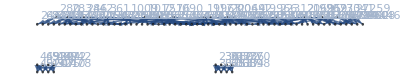

```mathematica
Graph[pr2,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
stubbornForm5[46942,"colortable"]//MatrixForm
```

(v124x35+v12x35x4 | 0
0 | v124x35+v12x35x4
v124x35 | v12x35x4
0 | v124x35+v12x35x4
0 | v124x35+v12x35x4
v124x35 | v12x35x4
0 | v124x35+v12x35x4
0 | v124x35+v12x35x4
v124x35+v12x35x4 | 0
0 | v124x35+v12x35x4)